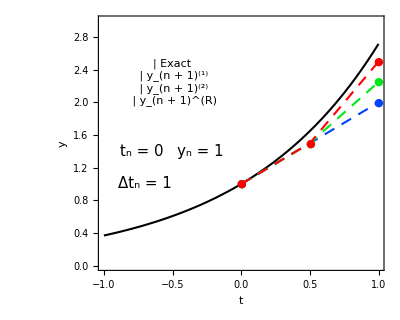

step_doubling.pdf

```mathematica
t0=0.0;
dt=1.0;
y0=Exp[t0];
t1=t0+dt;
tmid=t0+dt/2;
y1=y0+dt*y0;
ymid=y0+dt*y0/2;
y2=ymid+dt*ymid/2;
yR=2*y2-y1;

black={Black,AbsoluteThickness[1.5]};
red={Red,AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};
blue={Blend[{Blue,Cyan},0.25],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};
green={Blend[{Blue,Green},0.9],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};
purple={Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[1.5]};
t0Label=Style["t_n = 0",FontSize->15,FontFamily->"Arial",Black];
y0Label=Style["y_n = 1",FontSize->15,FontFamily->"Arial",Black];
dtLabel=Style["Δt_n = 1",FontSize->15,FontFamily->"Arial",Black];

legend=Panel[Grid[{{Graphics[{Directive[Black,AbsoluteThickness[2.]],Line[{{0,0},{1,0}}]},ImageSize->27,AspectRatio->0.5],Style["Exact",FontSize->15,FontFamily->"Arial"]},{Graphics[{Directive[blue[[1]],AbsoluteDashing[{8,6}],AbsoluteThickness[2.]],Line[{{0,0},{1,0}}]},ImageSize->27,AspectRatio->0.5],Style["y_(n + 1)^(1)",FontSize->15,FontFamily->"Arial"]},
{Graphics[{Directive[green[[1]],AbsoluteDashing[{8,6}],AbsoluteThickness[2.]],Line[{{0,0},{1,0}}]},ImageSize->27,AspectRatio->0.5],Style["y_(n + 1)^(2)",FontSize->15,FontFamily->"Arial"]},
{Graphics[{Directive[red[[1]],AbsoluteDashing[{8,6}],AbsoluteThickness[2.]],Line[{{0,0},{1,0}}]},ImageSize->27,AspectRatio->0.5],Style["y_(n + 1)^(R)",FontSize->15,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];

Show[{{
Plot[Exp[x],{x,-dt,dt},PlotRange->{0,3},PlotStyle->black,AspectRatio->0.8,Frame->True,FrameStyle->Black,BaseStyle->13,FrameLabel->{Style["t",FontFamily->"Arial",FontSize->14],Style["y",FontFamily->"Arial",FontSize->14]},Axes->None,Epilog->{Inset[t0Label,{-0.725,1.4}],Inset[y0Label,{-0.3,1.4}],Inset[dtLabel,{-0.7,1}],Inset[legend,{-0.5,2.25}]},ImageSize->400],

ListPlot[{{t0,y0},{t1,y1}},Joined->True,PlotMarkers->"●",PlotStyle->blue],
ListPlot[{{t0,y0},{tmid,ymid}, {t1,y2}},Joined->True,PlotMarkers->"●",PlotStyle->green],
ListPlot[{{t0,y0},{tmid,ymid},{t1,yR}},Joined->True,PlotMarkers->"●",PlotStyle->red]
}}]

Export["step_doubling.pdf",%]
```